```mathematica
Clear[x,y]
f[E_,L_] := Tan[L/2((2 * m * E)/hbar^2)^(1/2)];
g[E_, V_]:= ((V- E)/E)^(1/2);
fE [E_,L_] := D[f[x,y],x] /.{x->E, y->L};
fL[E_,L_] := D[f[x,y],y]/.{x->E, y->L};
gE [E_,V_] := D[g[x, y],x]/.{x->E, y->V};
gV [E_,V_] := D[g[x, y],y]/.{x->E, y->V};
LImportance[E_, L_, V_] := 1/(fE[E, L] + gE[E, V])*L/E*fL[E,L];
VImportance[E_, L_, V_] := 1/(fE[E, L] + gE[E, V])*V/E*gV[E,V];
Ratio[E_,L_,V_]:= LImportance[E,L,V]/VImportance[E,L,V];
Ratio1[E_, L_,V_]:= L/V * fL[E,L]/gV[E,V]
```

```mathematica
a = 1.5;
hbar = QuantityMagnitude[UnitConvert[Quantity[1,"ReducedPlanckConstant"]]];
γC = (UnitConvert[Quantity[200 , "Picoseconds"]])^-1;
γR = UnitConvert[Quantity[4.0 * 0.5, "Millielectronvolts" / "ReducedPlanckConstant"]];
R = UnitConvert[Quantity[0.05, "Millielectronvolts" * ("Micrometers")^2 / "ReducedPlanckConstant"]];
gC = UnitConvert[Quantity[2.0, "Millielectronvolts"*("Micrometers")^2]];
gR = 2.0 * gC ;
m = UnitConvert[Quantity[10^-3, "ElectronMass"]];
L = UnitConvert[Quantity[20, "Micrometers"]];
V = UnitConvert[(1/R) * (gR*γC + gC*γR*(a-1))];
CompatibleUnitQ[V, Quantity[1, "Joule"]]
m = QuantityMagnitude[m];
V = QuantityMagnitude[V];
L = QuantityMagnitude[L];

(*Define Some characteristic masses, lengths, and energies*)
Subscript[L, 0] = L;
Subscript[m, 0] = m;
Subscript[E, 0] = V;
(*This is the scaled version of Subscript[L, 2]*)
Subscript[L, 2] = (Sqrt[(Subscript[m, 0] * Subscript[E, 0])/hbar^2])^-1/Subscript[L, 0]
```

True

0.00217516

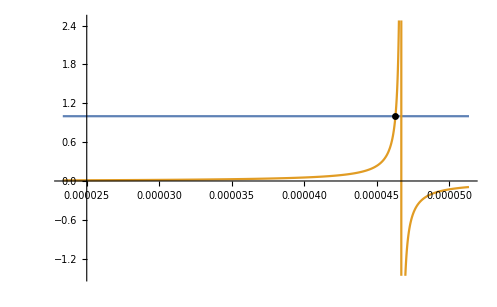

1300.3

```mathematica
b =1;
Ẽ= (g/.FindRoot[(1 - b * 0.5*g)^(1/2)== (b * g)^(1/2)* Tan[1/Subscript[L, 2] * (b * g)^(1/2)/2], {g, 0.9*(Pi*Subscript[L, 2])^2/b}]) / b;
(*Ẽ = 0.18*10^-4;*)
Plot[{(1-g)^(1/2),  (g)^(1/2)*Tan[1/Subscript[L, 2]*g^(1/2)/2]}, {g, 0.5*(Pi*Subscript[L, 2])^2,1.1* (Pi * Subscript[L, 2])^2}, Epilog->{PointSize[0.01], Point[{Ẽ, (Ẽ)^(1/2)*Tan[1/Subscript[L, 2]* (Ẽ)^(1/2)/2]}]}]
e = Subscript[E, 0] * Ẽ;
2 * L * Sqrt[(2 * m * (V-e))/hbar^2]
```

```mathematica
k̃ = (Ẽ)^(1/2)
α̃ = (1 - Ẽ)^(1/2)
k = e^(1/2)
```

0.00302285

0.999995

6.84739×10^-13

```mathematica
v = 0*10^-1;
La = L + v*L;
Va = V + v*V;
ea = e+ V*e;
Ratio[e, La, Va]
LImportance[e,La,Va]
VImportance[e,La,Va]
```

0.0841591

-0.087856

-1.04393

```mathematica
k = (2 * m * e)^(1/2)/hbar;
α = (2 * m * (V-e))^(1/2)/hbar;
A = (1/2*(L + Sin[k*L]/k) + 1/α*(Cos[(k * L)/2])^2)^(-1/2);
B = A * Cos[(k * L)/2]*Exp[(α*L)/2];
2*(Integrate[A^2*Cos[k*x]^2, {x, 0, L/2}] + Integrate[B^2*Exp[-2*α*x],{x, L/2, ∞}])
lImpPert [L_, V_, en_]:= (A^2*V*L)/(2*en)(1 + Cos[k*L])
vImpPert [L_, V_, en_]:= (B^2*V)/(2*α*en)Exp[-α * L]
pertRatio1[L_, V_, en_] := lImpPert[L,V, en]/vImpPert[L,V, en]
pertRatio2[L_,V_, en_] := 2 * L * Sqrt[(2 * m * (V-en))/hbar^2]
pertRatio1[L,V,e]
pertRatio2[L,V,e]
lImpPert[L,V,e]
vImpPert[L,V,e]
```

0.998259

1040.23

1040.23

12547.1

12.0619

8.10044

0.0271804

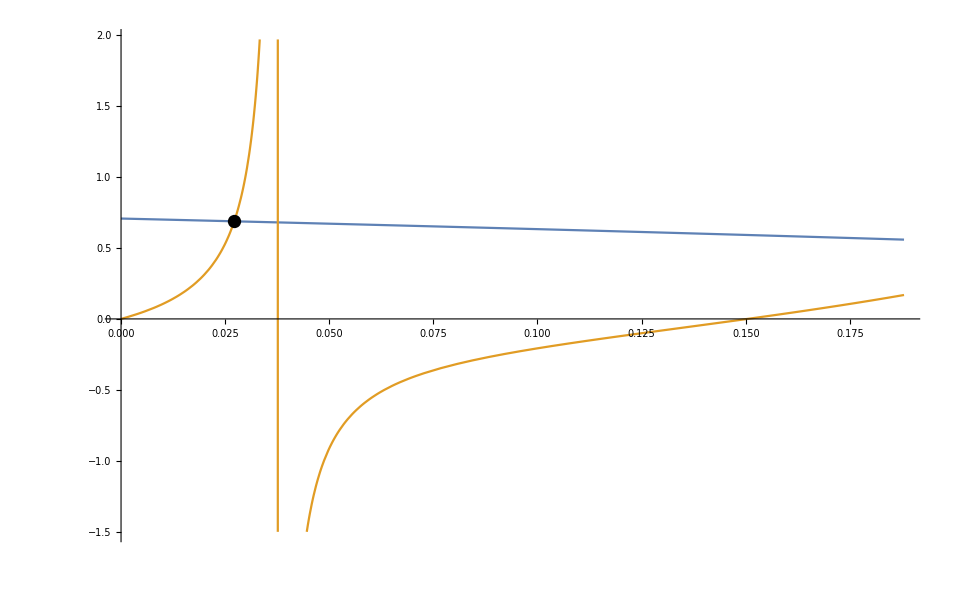

```mathematica
hbar = UnitConvert[Quantity[1,"ReducedPlanckConstant"]];
m = UnitConvert[Quantity[10^-4, "ElectronMass"]];

(*Define Some characteristic masses, lengths, and energies*)
L0 = Quantity[10, "Micrometers"];
m0 = m;
E0 =UnitConvert[Quantity[1, "Millielectronvolts"], "Millielectronvolts"];
(*This is the scaled version of Subscript[L, 2]*)
 k=UnitConvert[ (Sqrt[(2*m0 * E0)/hbar^2]*L0)/2];
k
(* L and V are in units of Subscript[L, o] and Subscript[E, 0] respectively*)
L = 1;
V = 0.5;
e = Re[g/.FindRoot[(V -   g)^(1/2)== (g)^(1/2)* Tan[k *L*(g)^(1/2)], {g, 0.9*(Pi/2* 1/(k * L))^2}]]
Plot[{(V-g)^(1/2),  (g)^(1/2)*Tan[k * L * g^(1/2)]}, {g, 0.0*(Pi/2* 1/(k * L))^2,5.0* (Pi/2* 1/(k * L))^2}, Epilog->{PointSize[0.01], Point[{e, (e)^(1/2)*Tan[k * L * (e)^(1/2)]}]}]
```

```mathematica
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
Energy[x_, y_]:=Re[ g/.FindRoot[(y -   g)^(1/2)== (g)^(1/2)* Tan[k *x*(g)^(1/2)], {g, 0.9*(Pi/2* 1/(k * x))^2}]]
hbar = UnitConvert[Quantity[1,"ReducedPlanckConstant"]];
m = UnitConvert[Quantity[10^-3, "ElectronMass"]];

(*Define Some characteristic masses, lengths, and energies*)
L0 = Quantity[10, "Micrometers"];
m0 = m;
E0 =UnitConvert[Quantity[1, "Millielectronvolts"], "Millielectronvolts"];
(*This is the scaled version of Subscript[L, 2]*)
 k=UnitConvert[ (Sqrt[(2*m0 * E0)/hbar^2]*L0)/2];
k
ns = 200;
(*x is L and y is V*)
xax  =Array[#&,ns,{0.1,10}];
yax = Array[#&,ns,{0.1,10}];
{xx,yy}=meshgrid[xax, yax];
zz = MapThread[Energy ,{xx, yy}, 2];
(*Check which elements are wrong*)
errors = Select[Flatten[Chop[MapThread[Abs[(#2 - #3)^(1/2) - (#3)^(1/2)*Tan[k * #1 * (#3)^(1/2)]]&, {xx, yy, zz}, 2], 10^-6]], #>0&]
ListPlot3D[Flatten[MapThread[{#1, #2, #3}&, {xx,yy,zz}, 2] , 1], 
AxesLabel->{"L *"L0,"V * "E0, "E *"E0}]
(*xx⟦1, 4⟧
yy[[1, 4]]
zz[[1, 4]]
Energy[xx[[1, 4]], yy[[1, 4]]]*)
```

25.6158

{}

-Graphics3D-

```mathematica
A = {{aa, bb},{cc,dd}};
A//MatrixForm
B = {{ee, ff}, {gg, hh}};
B // MatrixForm
c = {{ii, jj}, {kk, ll}};
h[a_,b_, c_] := {a, b, c}
Flatten[MapThread[{#1, #2, #3}&, {A,B,c}, 2] , 1]
```

(aa | bb
cc | dd)

(ee | ff
gg | hh)

{{aa,ee,ii},{bb,ff,jj},{cc,gg,kk},{dd,hh,ll}}

```mathematica
Array[#&,10,{-1.0,1}]
```

{-1.,-0.777778,-0.555556,-0.333333,-0.111111,0.111111,0.333333,0.555556,0.777778,1.}

```mathematica
Re[4]
```

4